## Практическое задание №4 Дунаев Виктор Андреевич 3 Курс, 6 Группа

## Task 1

```mathematica
one =(2x y+4 x^2-2x y^2)^3
```

(4 x^2+2 x y-2 x y^2)^3

```mathematica
o1 =Factor[one]
```

8 x^3 (2 x+y-y^2)^3

```mathematica
Length[o1]
```

3

```mathematica
o2=FactorTerms[one,y]
```

-8 x^3 (-8 x^3-12 x^2 y-6 x y^2+12 x^2 y^2-y^3+12 x y^3+3 y^4-6 x y^4-3 y^5+y^6)

```mathematica
Length[o2]
```

3

```mathematica
o3=FactorTerms[one]
```

8 (8 x^6+12 x^5 y+6 x^4 y^2-12 x^5 y^2+x^3 y^3-12 x^4 y^3-3 x^3 y^4+6 x^4 y^4+3 x^3 y^5-x^3 y^6)

```mathematica
Length[o3]
```

2

```mathematica
o4=Collect[one, x]
```

64 x^6+x^5 (96 y-96 y^2)+x^4 (48 y^2-96 y^3+48 y^4)+x^3 (8 y^3-24 y^4+24 y^5-8 y^6)

```mathematica
Length[o4]
```

4

## Task 2

```mathematica
equ = (x^2+2*x+1)/((2+x)(3+x))
```

(1+2 x+x^2)/((2+x) (3+x))

```mathematica
Expand[equ]
```

1/((2+x) (3+x))+(2 x)/((2+x) (3+x))+x^2/((2+x) (3+x))

```mathematica
Factor[equ]
```

(1+x)^2/((2+x) (3+x))

```mathematica
Apart[equ]
```

1+1/(2+x)-4/(3+x)

```mathematica
PolynomialGCD[Numerator[equ], Denominator[equ]]
```

1

```mathematica
PolynomialLCM[Numerator[equ],Denominator[equ]]
```

(2+x) (3+x) (1+2 x+x^2)

## Task 3

```mathematica
Clear[a, b, x, y, z]
```

```mathematica
ini = a^b-a^2+2*b^2-3a b+1
```

1-a^2+a^b-3 a b+2 b^2

```mathematica
ini/.{a->x, b-> (x+y^2)}
```

1-x^2+x^(x+y^2)-3 x (x+y^2)+2 (x+y^2)^2

## Task 4

```mathematica
expr = (x+1+x*y)^2
```

(1+x+x y)^2

```mathematica
expr /. y->3x-2b/. x->(b+2)
```

(3+b+(2+b) (-2 b+3 (2+b)))^2

## Task 5

```mathematica
(* Найти пределы *)
```

```mathematica
Limit[(x^2-4)/(x-2),x->2]
```

4

```mathematica
Limit[1/(x-5)-10/(x^2-25),x->5]
```

1/10

```mathematica
Limit[Sin[x]/x,x->0]
```

1

```mathematica
Limit[((x+2y)/x)^x,x->Infinity ]
```

ⅇ^(2 y)

```mathematica
Limit[(1+1/x)^(2x+1),x->Infinity]
```

ⅇ^2

```mathematica
Limit[Tan[x]/x,x->0]
```

1

```mathematica
(* Разложить в степенной ряд*)
```

```mathematica
row[x_] = Series[ⅇ^(-a x)(1+2Cos[a x]), {x, 0, 5}]
```

3-3 a x+(a^2 x^2)/2+(a^3 x^3)/2-(7 a^4 x^4)/24+(7 a^5 x^5)/120+O[x]^6

```mathematica
3-3 x+x^2/2+x^3/2-(7 x^4)/24+(7  x^5)/120
```

3-3 x+x^2/2+x^3/2-(7 x^4)/24+(7 x^5)/120

```mathematica
ec = Normal[row[x]]/.a-> 1
```

3-3 x+x^2/2+x^3/2-(7 x^4)/24+(7 x^5)/120

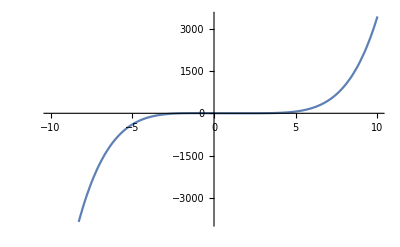

```mathematica
Plot[ec, {x, -10, 10}]
```

```mathematica
D[row[x], a]
```

-3 x+a x^2+(3 a^2 x^3)/2-(7 a^3 x^4)/6+(7 a^4 x^5)/24+O[x]^6

```mathematica
FourierSeries[Exp[-a x](1+2Cos[a x]),Sin[Pi(2n+1)x/2],7]
```

ⅇ^(-a x) (FourierSeries[1,Sin[1/2 (1+2 n) π x],7]+2 FourierSeries[Cos[a x],Sin[1/2 (1+2 n) π x],7])

```mathematica
row[x]
```

3-3 a x+(a^2 x^2)/2+(a^3 x^3)/2-(7 a^4 x^4)/24+(7 a^5 x^5)/120+O[x]^6

```mathematica
Manipulate[Plot[{ⅇ^(-a x)(1+2Cos[a x]), ec}, {x, 2, 3}], {{a, 1, "a"}, 0, 2}]
```

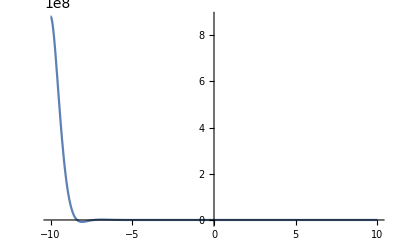

```mathematica
Plot[ⅇ^(- 2x)(1+2Cos[ 2x]), {x, -10, 10}, PlotRange->All]
```

```mathematica
(* Найти площадь криволинейной трапеции *)
```

```mathematica
Clear[x];
```

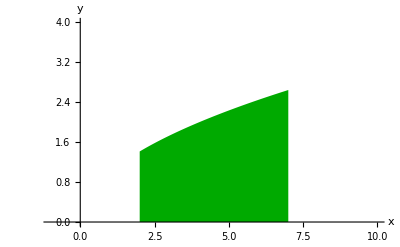

```mathematica
Plot[x^(1/2),{x,2,7}, AxesLabel->{x, y}, AxesStyle->Arrowheads[0.03], PlotStyle-> None, Filling->Bottom, FillingStyle-> Darker[Green], PlotRange->{{-1,10},{0,4}}]
```

```mathematica
∫_2^7 x^(1/2)ⅆx
```

2/3 (-2 √2+7 √7)

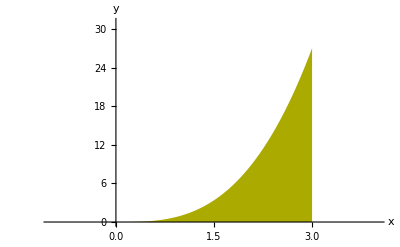

```mathematica
Plot[x^3,{x,0,3}, AxesLabel->{x, y}, AxesStyle->Arrowheads[0.03],PlotStyle-> None, Filling->Bottom, FillingStyle-> Darker[Yellow], PlotRange->{{-1,4},{0,3^3+4}}]
```

```mathematica
∫_0^3 x^3 ⅆx
```

81/4

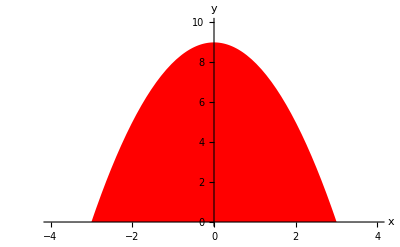

```mathematica
Plot[9-x^2,{x,-3,3}, AxesLabel->{x, y}, AxesStyle->Arrowheads[0.03],PlotStyle-> None, Filling->Bottom, FillingStyle-> Red, PlotRange->{{-4,4},{0,10}}]
```

```mathematica
∫_-3^3 (9-x^2)ⅆx
```

36

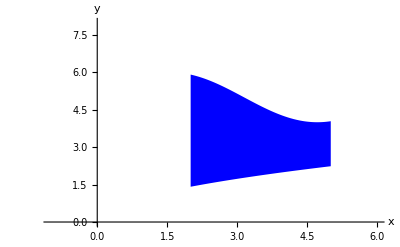

```mathematica
Plot[{Sin[x]+5, x^(1/2)},{x,2,5}, AxesLabel->{x, y}, AxesStyle->Arrowheads[0.03],Filling->{1->{2}},PlotStyle-> None,FillingStyle-> Blue, PlotRange->{{-1,6},{0,8}}]
```

```mathematica
∫_2^5 (Sin[x]+5)ⅆx - ∫_2^5 x^(1/2)ⅆx
```

15-2/3 (-2 √2+5 √5)+Cos[2]-Cos[5]

```mathematica
(* Написать фукцию Dif *)
```

```mathematica
Dif[expression_]:=
(
result = 0;
For[i=1, i≤ Length[expression], i++, 
result+= Dif[expression⟦i⟧]
];
expression⟦1⟧
)
```

```mathematica
Dif[x y^2]
```

Part::partd: Part specification x⟦1⟧ is longer than depth of object.

Part::partd: Part specification y⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

```mathematica
toSumList[expression_]:=
(
exp = koef1 +koef2+expression;
sumList = {};
For[i=3, i≤  Length[exp], i++, 
AppendTo[sumList, exp⟦i⟧];
];
sumList
)
```

```mathematica
toSumList[o4]
```

{o4}

```mathematica
sDiff[expression_]:=
(
If[NumericQ[expression], result=0];
If[TrueQ[expression== Sin], result=0];
)
```

```mathematica
mult[expression_]:= 
(
sDiff[expression⟦1⟧]*expression⟦2⟧+sDiff[expression⟦2⟧]*expression⟦1⟧
)
```

```mathematica
Length[ o1*mulkoef]
```

2

```mathematica
Collect[x^2*Sin[x], x]
```

x^2 Sin[x]

```mathematica
koef1 +koef2+(x+1+x*y)^2
```

koef1+koef2+(1+x+x y)^2

```mathematica
tst[sw_]:=
(
strSW = ToString[sw]

)
```

```mathematica
tst[Sin[x^2]]
```

2
Sin[x ]

```mathematica
NumberQ[Sin[1]]
```

False